```mathematica
Table[ShowGraph5Least[k],{k,amigos}]
```

{-Graphics-294131,-Graphics-207731,-Graphics-272291,-Graphics-229331,-Graphics-206951}

```mathematica
Table[ShowGraph5Least[k],{k,{starKey}}]
```

{-Graphics-88595}

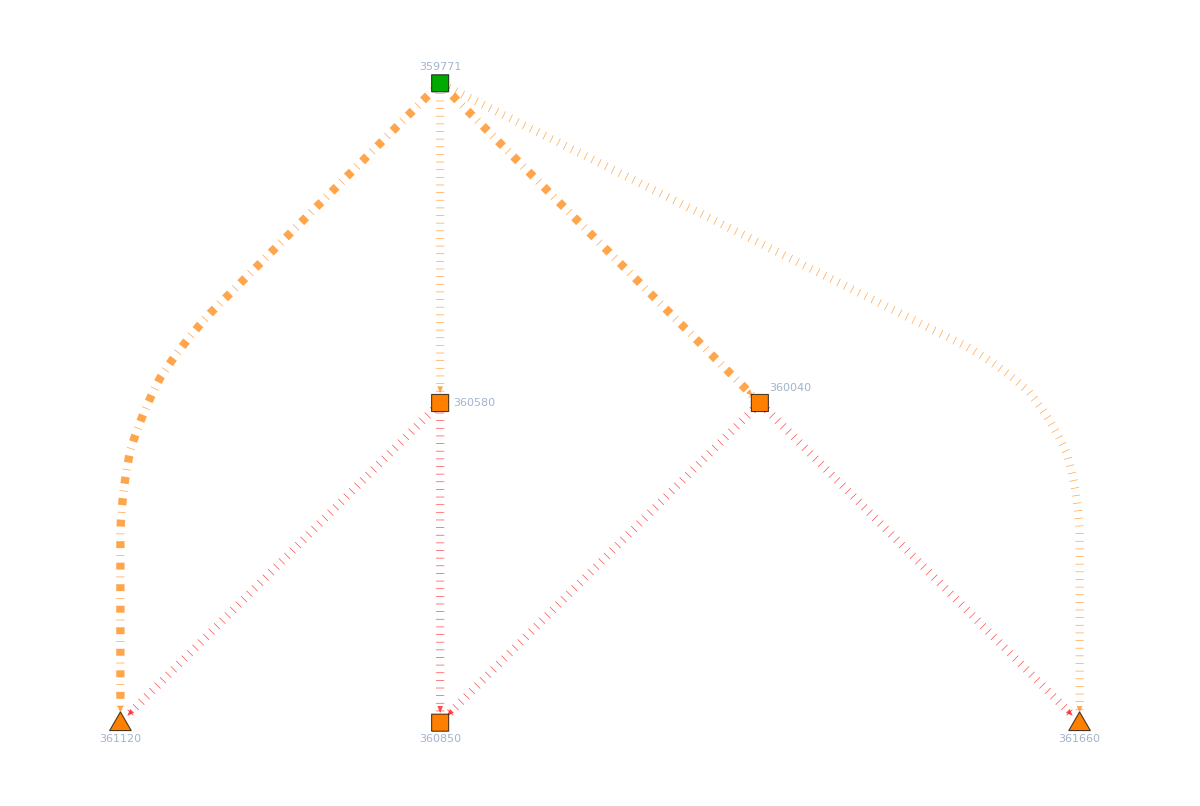

```mathematica
With[{root=alfaKey},With[{h=Graph[Traverse[root], GraphLayout->"LayeredDigraphEmbedding", ImageSize->1200]},
Graph[h,  ImageSize->1200,EdgeStyle->Map[#->Directive[Orange,Dashed,Thick]&,toDelete]]]]
```